lpw

```mathematica
(* Mathematica notebook for spectra (to compare with simulation). Following [Esarey]'s paper in sections A. and B. analysis of harmonics spectra requires spectra "boris.txt" from a test-particle or particle-in-cell simulation.

  date : 05/04/2019
  author: Óscar L. Amaro
*)
```

Intro

```mathematica
(*Parameters*)
γ0=5; (*p. 48*)
a0=1;

β0=√(1-1/γ0^2); (*normalizations*)
ω0=2;
k0=ω0;

h0=γ0(1+β0); (* p.3006 (8c) se se excluir Φ...*)
M0=h0^2/(1+a0^2/2);
η0=100;(*controls fineness of spectrum*)

β1=(1-1/M0)/2; 
r1=a0 / (h0 k0); (*p. 3006 (16a)*)
z1=-a0^2 / (8 h0^2 k0);
β1=(1-1/M0)/2; (*p.3006 16c*)
(*Functions p. 3008*)
kbar=Function[{ω,θ,n},ω(1-β1(1+Cos[θ]))-n k0];(*(30a)*)
```

A. Linear polarization p. 3007

```mathematica
(*alpha*)
αz=Function[{θ,ϕ,n},(n a0^2 (1+Cos[θ]))/(8 h0^2 (1-β1 (1+Cos[θ])))];(*(38a)*)
αx=Function[{θ,ϕ,n},(n a0 Sin[θ]Cos[0])/(h0 (1-β1(1+Cos[θ])))];(*(38b)*)
(*C*)
sumlim=20; (*parameter that controls the sum*)
Cx=Function[{θ,ϕ,n},
k0 r1 Sum[N[    (-1)^m BesselJ[m,αz[θ,0,n]] (BesselJ[n-2 m-1,αx[θ,0,n]]+BesselJ[n-2 m +1,αx[θ,0,n]])    ],
{m,-sumlim,sumlim}]];(*(37a)*)

Cz=Function[{θ,ϕ,n},
2 Sum[N[   (-1)^m  BesselJ[m,αz[θ,0,n]] (β1*BesselJ[n-2 m,αx[θ,0,n]] +k0 z1 (
BesselJ[n-2 m -2,αx[θ,0,n]]+BesselJ[n-2 m +2,αx[θ,0,n]] ))  ],
{m,-sumlim,sumlim}]] ;(*(37b)*)

(*main*)
dIdωdΩ=Function[{ω,θ,ϕ},
ω^2/(4 π^2) Sum[ (Sin[kbar[ω,θ,n] η0 ]/(kbar[ω,θ,n] η0))^2(Cx[θ,0,n]^2(1-Sin[θ]^2 Cos[ϕ]^2)+Cz[θ,0,n]^2 Sin[θ]^2 - Cx[θ,0,n] Cz[θ,0,n] Sin[2θ]Cos[ϕ]) 
,{n,1,40}]]; (*(36*)
```

```mathematica
(*plot against simulation*)
wmax=5;
lst=ParallelTable[{y,dIdωdΩ[4 γ0^2 ω0 y,N[π/10],0]/.ω->( 4 γ0^2 ω0  y)},{y,0.01,wmax,wmax/2000}];
```

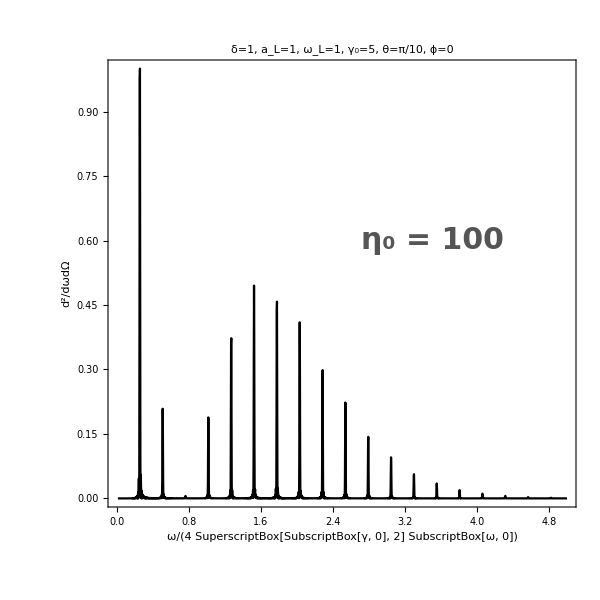

```mathematica
Max[lst[[All,2]]];
lst[[All,2]]/=Max[lst[[All,2]]];
grp1=ListPlot[lst,AspectRatio->1,Joined->True,Frame->True,FrameLabel->{"ω/(4 SuperscriptBox[SubscriptBox[γ, 0], 2] SubscriptBox[ω, 0])","d^2/dωdΩ"},PlotLabel->Text[Style["δ=1, a_L="<>ToString[a0] <>", ω_L=1, γ_0=5, θ=π/10, ϕ=0",30,Bold]],FrameStyle->Directive[Bold,FontSize->30],PlotStyle->Directive[Black,Opacity[1]],ImageSize->600,PlotRange->{{0,5},{0,1}}];
Show[{grp1,Graphics[{Text[Style[Style["η_0 = 100",Darker[Gray]] ,FontSize->30,Bold],{3.5,0.6}]}]}]
```

```mathematica
Export["esarey.txt",lst]
```

esarey.txt

Compare with simulation

```mathematica
mat=Import["boris.txt","Table"];
mat=Flatten[mat];
w=Import["dataw.txt","Table"];
w=Flatten[w];
```

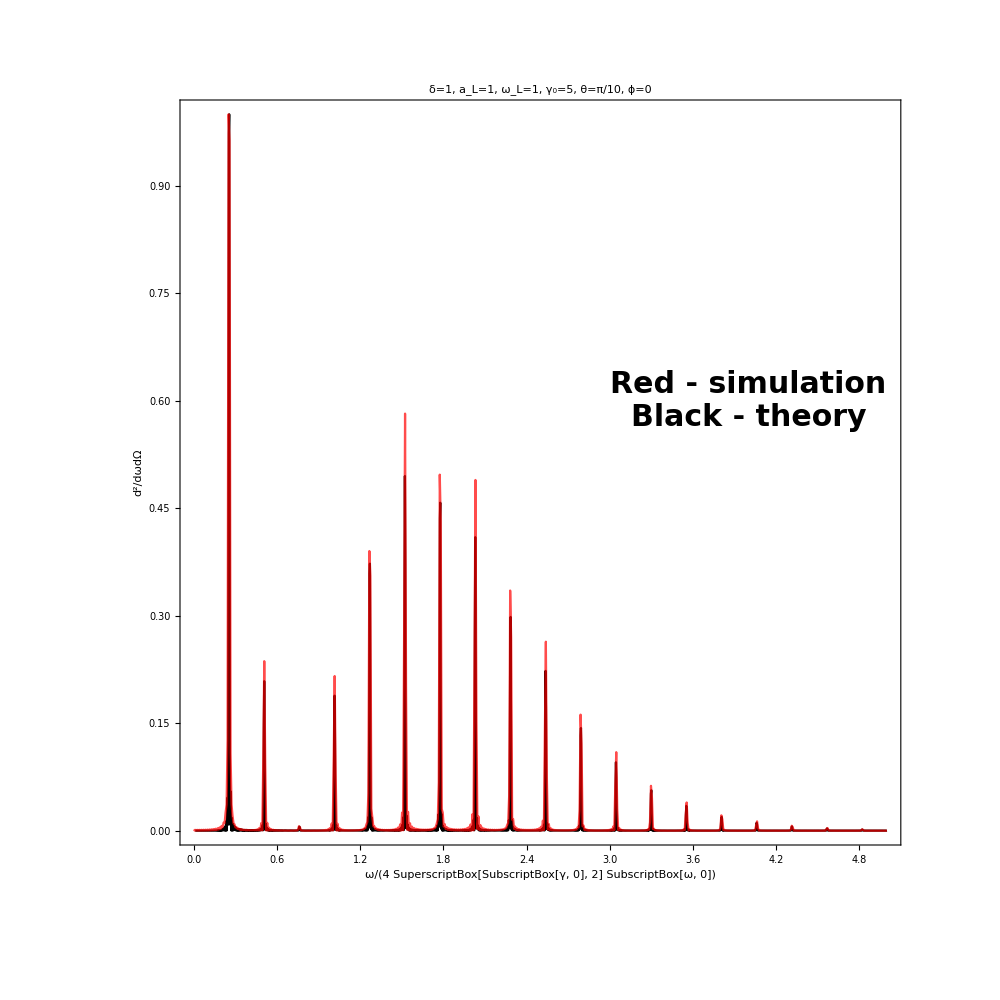

```mathematica
grp2=ListPlot[Transpose[{w/(4*γ0^2),mat/Max[mat]}],ImageSize->Medium,AspectRatio->1,Joined->True,Frame->True,FrameLabel->{"ω/(4 SuperscriptBox[SubscriptBox[γ, 0], 2] SubscriptBox[ω, 0])","d^2/dωdΩ"},PlotRange->{{0,2.5},{0,1}},PlotStyle->{Black,Directive[Red,Opacity[0.7]]},ImageSize->600];
Show[{grp1,grp2,Graphics[{Text[Style[Style["Red",Red] "- simulation\nBlack - theory",FontSize->30,Bold],{4,0.6}]}]},ImageSize->1000]
```

B. Circular polarization p. 3010

```mathematica
α=Function[{n,θ},(n(a0/√2)Sin[θ])/(h0(1-β1(1+Cos[θ])))];
dIdωdΩ=Function[{ω,θ,ϕ},
ω^2/π^2 Sum[ N[(Sin[kbar[ω,θ,n] η0 ]/kbar[ω,θ,n])^2((Cos[θ]-β1(1+Cos[θ]))^2/Sin[θ]^2 BesselJ[n,α[n,θ]]^2+(k0^2 r1^2)/2((1/2 (BesselJ[-1+n,x]-BesselJ[1+n,x]))/.x->α[n,θ])^2)]
,{n,1,80}]]; 
(*(36*)
```

```mathematica
lst=ParallelTable[{y,dIdωdΩ[4 γ0^2 y,N[π/10],0]/.ω->( 4 γ0^2 y)},{y,0.01,10,10/6000}];
```

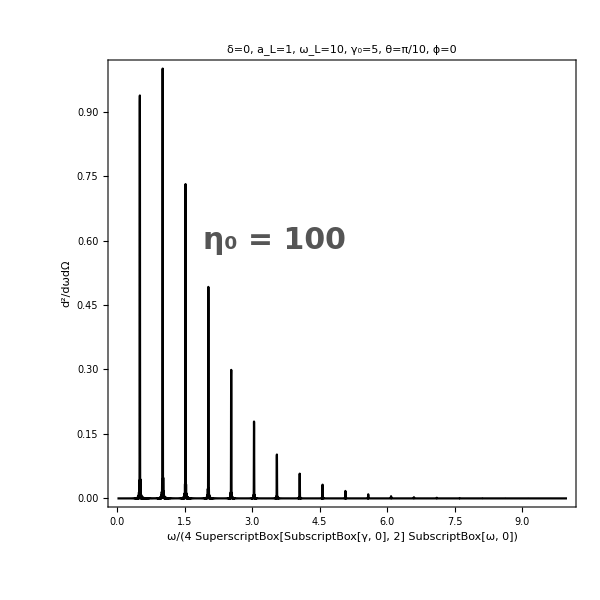

```mathematica
Max[lst[[All,2]]];
lst[[All,2]]/=Max[lst[[All,2]]];
grp1=ListPlot[lst,AspectRatio->1,Joined->True,Frame->True,FrameLabel->{"ω/(4 SuperscriptBox[SubscriptBox[γ, 0], 2] SubscriptBox[ω, 0])","d^2/dωdΩ"},PlotLabel->Text[Style["δ=0, a_L="<>ToString[a0] <>", ω_L=10, γ_0=5, θ=π/10, ϕ=0",30,Bold]],FrameStyle->Directive[Bold,FontSize->30],PlotStyle->Directive[Black,Opacity[1]],ImageSize->600,PlotRange->{{0,10},{0,1}}];
Show[{grp1,Graphics[{Text[Style[Style["η_0 = 100",Darker[Gray]] ,FontSize->30,Bold],{3.5,0.6}]}]}]
```

Compare with simulation

```mathematica
mat=Import["boris.txt","Table"];
mat=Flatten[mat];
w=Import["dataw.txt","Table"];
w=Flatten[w];
```

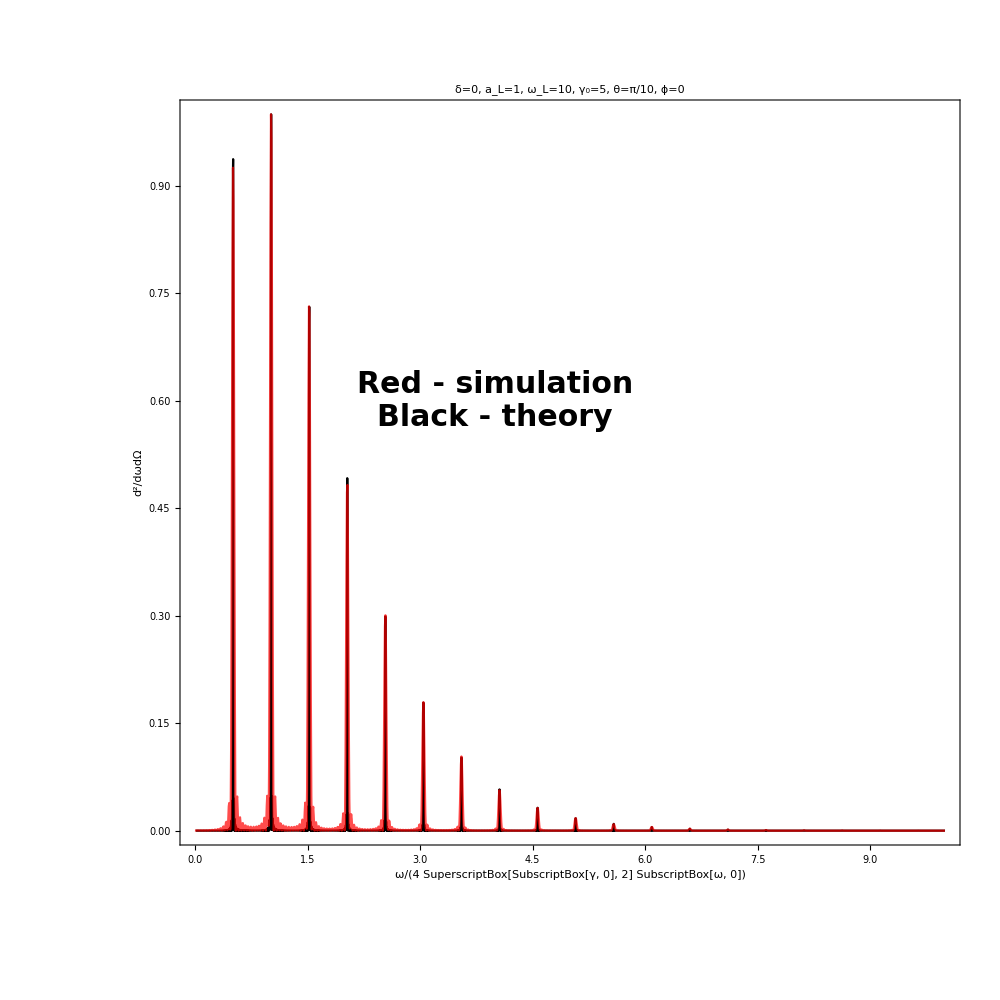

```mathematica
grp2=ListPlot[Transpose[{w/(4*γ0^2),mat/Max[mat]}],ImageSize->Medium,AspectRatio->1,Joined->True,Frame->True,FrameLabel->{"ω/(4 SuperscriptBox[SubscriptBox[γ, 0], 2] SubscriptBox[ω, 0])","d^2/dωdΩ"},PlotRange->{{0,2.5},{0,1}},PlotStyle->{Black,Directive[Red,Opacity[0.7]]},ImageSize->600];
Show[{grp1,grp2,Graphics[{Text[Style[Style["Red",Red] "- simulation\nBlack - theory",FontSize->30,Bold],{4,0.6}]}]},ImageSize->1000]
```